```mathematica
<<MaTeX`
ClearAll[plotColors];
plotColors::usage="plotColors[plotType,plotTheme] gives a list of the colors used in a plot when several curves are drawn. Here plotType is, for example, Plot or ListLogPlot while plotTheme may be \"Scientific\", \"Classic\" etc.";
plotColors[plotType_,plotTheme_]:=("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme[plotTheme,plotType]))/.Directive[x_,__]:>x;
pltcolors=plotColors[ListLinePlot,"Scientific"];
```

### MaTeX

```mathematica
magnificationaxes=1.;
magnificationlegends=1.;
latex411=MaTeX["D^+",Magnification->magnificationlegends,ContentPadding->False];
latex431=MaTeX["D_s^+",Magnification->magnificationlegends,ContentPadding->False];
latex411bar=MaTeX["D^-",Magnification->magnificationlegends,ContentPadding->False];
latex431bar=MaTeX["D_s^-",Magnification->magnificationlegends,ContentPadding->False];
latexpythia=MaTeX["\\text{PYTHIA8}",Magnification->magnificationlegends,ContentPadding->False];
latexgaussian=MaTeX["\\text{Gaussian}",Magnification->magnificationlegends,ContentPadding->False];
latexgaussian=MaTeX["e^{-ax_F^2}",Magnification->magnificationlegends,ContentPadding->False];
latexold=MaTeX["(1-|x_F|)^n",Magnification->magnificationlegends,ContentPadding->False];
latexoldb=MaTeX["b=1.08",Magnification->magnificationlegends,ContentPadding->False];
latexnewb=MaTeX["b=0.63",Magnification->magnificationlegends,ContentPadding->False];
xlabel=MaTeX["x_F",Magnification->magnificationaxes,ContentPadding->False];
xlabelpt2=MaTeX["pT^2 (\\text{GeV}^2)",Magnification->magnificationaxes,ContentPadding->False];
ylabel=MaTeX["info*\\frac{d\\sigma}{dx_F}",Magnification->magnificationaxes,ContentPadding->False];
ylabelpt2=MaTeX["info*\\frac{d\\sigma}{dpT^2}",Magnification->magnificationaxes,ContentPadding->False];
```

## Import rawdata, make histos & datatables

```mathematica
rawdataxf={};
AppendTo[rawdataxf,Import[NotebookDirectory[]<>"xfdata411.dat"][[1]]];
AppendTo[rawdataxf,Import[NotebookDirectory[]<>"xfdata431.dat"][[1]]];
AppendTo[rawdataxf,Import[NotebookDirectory[]<>"xfdata411bar.dat"][[1]]];
AppendTo[rawdataxf,Import[NotebookDirectory[]<>"xfdata431bar.dat"][[1]]];
rawdatapt2={};
AppendTo[rawdatapt2,Import[NotebookDirectory[]<>"pt2data411.dat"][[1]]];
AppendTo[rawdatapt2,Import[NotebookDirectory[]<>"pt2data431.dat"][[1]]];
AppendTo[rawdatapt2,Import[NotebookDirectory[]<>"pt2data411bar.dat"][[1]]];
AppendTo[rawdatapt2,Import[NotebookDirectory[]<>"pt2data431bar.dat"][[1]]];
```

```mathematica
nbins=45;
bspecxf={};
bspecpt2={};
histolistxf={};
histolispt2={};
xftable={};
pt2table={};
Do[
bwidth=(Max[rawdataxf[[k]]]-Min[rawdataxf[[k]]])/nbins;
AppendTo[bspecxf,{Table[Min[rawdataxf[[k]]]+bwidth*i,{i,0,nbins}]}];
AppendTo[histolistxf,HistogramList[rawdataxf[[k]],bspecxf[[k]]]];
factor=1/(Length@rawdataxf[[k]])/bwidth;
AppendTo[xftable,Table[{(histolistxf[[k,1,i]]+histolistxf[[k,1,i+1]])/2,histolistxf[[k,2,i]]*factor},{i,1,nbins}]];
bwidth=(Max[rawdatapt2[[k]]]-Min[rawdatapt2[[k]]])/nbins;
AppendTo[bspecpt2,{Table[Min[rawdatapt2[[k]]]+bwidth*i,{i,0,nbins}]}];
AppendTo[histolispt2,HistogramList[rawdatapt2[[k]],bspecpt2[[k]]]];
factor=1/(Length@rawdatapt2[[k]])/bwidth;
AppendTo[pt2table,Table[{(histolispt2[[k,1,i]]+histolispt2[[k,1,i+1]])/2,histolispt2[[k,2,i]]*factor},{i,1,nbins}]];
,{k,1,4}]
```

## Fit Data

```mathematica
tableid={411,431,-411,-431};
tablefita={};
tablefitb={};
tablea={};
tablesigmaa={};
tableb={};
tablesigmab={};
Do[
fitauxa=NonlinearModelFit[xftable[[i]],√(aa/Pi)Exp[-aa*x^2],{aa},{x}];
fitauxb=NonlinearModelFit[pt2table[[i]],bb*Exp[-bb*x],{bb},{x}];
AppendTo[tablefita,fitauxa];
AppendTo[tablefitb,fitauxb];
AppendTo[tablea,aa/.fitauxa["BestFitParameters"]];
AppendTo[tableb,bb/.fitauxb["BestFitParameters"]];
AppendTo[tablesigmaa,fitauxa["ParameterErrors"][[1]]];
AppendTo[tablesigmab,fitauxb["ParameterErrors"][[1]]];
,{i,1,4}]
MatrixForm[Table[{tableid[[i]],AccountingForm[tablea[[i]],10],AccountingForm[tablesigmaa[[i]],10],AccountingForm[tableb[[i]],10],AccountingForm[tablesigmab[[i]],10]},{i,1,4}]]
```

(411 | 15.19155426 | 0.1980987252 | 0.7224403738 | 0.01497588645
431 | 16.63400343 | 0.2861446859 | 0.6342406092 | 0.01082256447
-411 | 13.12607950 | 0.1710191446 | 0.9291049592 | 0.02083670673
-431 | 15.10032853 | 0.3517372639 | 0.8003448539 | 0.01885656305)

## Plots by flavour

### xF plots D431

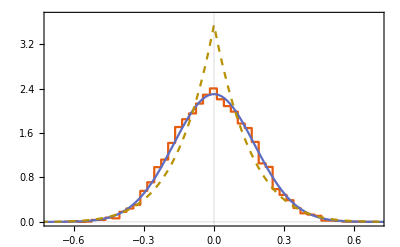

```mathematica
plotrange={{-0.7,0.7},{0,3.7}};
framelabel={xlabel,ylabel};
legends={latexpythia,latexgaussian,latexold};
plotlegends=Placed[LineLegend[{pltcolors[[1]],pltcolors[[2]],{Dashed,pltcolors[[8]]}},legends,Spacings->0.01,LegendLayout->{"Column",1},LegendMarkerSize->16
],{0.825,0.8}];
imagesize={{300},Automatic};
frametickstyle=Directive[Black];
imagepadding={{50,3},{40,1}};
a=tablea[[2]];
n=6.1;
text=Graphics[Text[latex431,Scaled[{0.1,0.9}]]];
listplot=ListStepPlot[{xftable[[2]]},Center,PlotStyle->{pltcolors[[1]]}];
newplot=Plot[√(a/Pi)Exp[-a*x^2],{x,-1,1},PlotStyle->pltcolors[[2]]];
oldplot=Plot[(n+1)/2*(1-Abs[x])^n,{x,-1,1},PlotStyle->{Dashed,pltcolors[[8]]}];
bg=Plot[{,,,},{x,-1,1},PlotTheme->"Scientific",PlotRange->plotrange,AspectRatio->1/GoldenRatio,PlotLegends->plotlegends,FrameLabel->framelabel,ImageSize->imagesize,ImagePadding->imagepadding,FrameTicksStyle->frametickstyle];
plotexp=Show[bg,listplot,newplot,oldplot]
Export["/home/sane/mainhnlchain/hnlchain/paperHNL/plots/plot-fit431xf.pdf",plotexp];
```

### pt2 plots D431

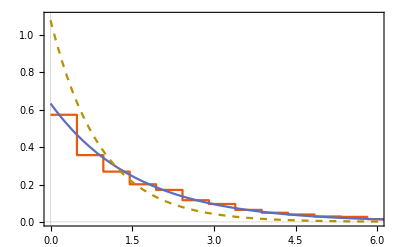

```mathematica
plotrange={{0,6},{0,1.1}};
framelabel={xlabelpt2,ylabelpt2};
legends={latexpythia,latexnewb,latexoldb};
plotlegends=Placed[LineLegend[{pltcolors[[1]],pltcolors[[2]],{Dashed,pltcolors[[8]]}},legends,Spacings->0.01,LegendLayout->{"Column",1},LegendMarkerSize->16
],{0.825,0.8}];
imagesize={{300},Automatic};
frametickstyle=Directive[Black];
imagepadding={{50,3},{40,1}};
a=16.6339541;
oldb=1.08;
newb=tableb[[2]];
text=Graphics[Text[latex431,Scaled[{0.1,0.9}]]];
listplot=ListStepPlot[{pt2table[[2]]},Center,PlotStyle->{pltcolors[[1]]},PlotRange->All];
oldplot=Plot[oldb*Exp[-oldb*x],{x,0,20},PlotStyle->{Dashed,pltcolors[[8]]},PlotPoints->200,PlotRange->All];
newplot=Plot[newb*Exp[-newb*x],{x,0,20},PlotStyle->pltcolors[[2]],PlotRange->All];
bg=Plot[{,,,},{x,0,1},PlotTheme->"Scientific",PlotRange->plotrange,AspectRatio->1/GoldenRatio,PlotLegends->plotlegends,FrameLabel->framelabel,ImageSize->imagesize,FrameTicksStyle->frametickstyle,ImagePadding->imagepadding];
plotexp=Show[bg,listplot,newplot,oldplot]
Export["/home/sane/mainhnlchain/hnlchain/paperHNL/plots/plot-fit431pt2.pdf",plotexp];
```

## Plots Dall

### xF plots-Dall

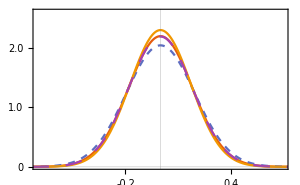

```mathematica
plotrange={{-0.7,0.7},{0.01,2.6}};
framelabel={xlabel,ylabel};
legends={latex411,latex411bar,latex431,latex431bar};
d411color=pltcolors[[1]];
d411barcolor=pltcolors[[2]];
d431color=pltcolors[[3]];
d431barcolor=pltcolors[[4]];
plotlegends=Placed[LineLegend[{d411color,{Dashed,d411barcolor},d431color,{Dashed,d431barcolor}},legends,Spacings->0.01,LegendLayout->{"Column",2},LegendMarkerSize->16
],{0.825,0.825}];
imagesize={300,Automatic};
frametickstyle=Directive[Black];
imagepadding={{60,3},{40,1}};
scalingfunctions={"Linear","Linear"};
a411=15.1914842;
a431=16.6339541;
a411bar=13.1260718;
a431bar=15.09998238;
newplot411=Plot[√(a411/Pi)Exp[-a411*x^2],{x,-1,1},PlotStyle->d411color,ScalingFunctions->scalingfunctions];
newplot411bar=Plot[√(a411bar/Pi)Exp[-a411bar*x^2],{x,-1,1},PlotStyle->{Dashed,d411barcolor},ScalingFunctions->scalingfunctions];
newplot431=Plot[√(a431/Pi)Exp[-a431*x^2],{x,-1,1},PlotStyle->d431color,ScalingFunctions->scalingfunctions];
newplot431bar=Plot[√(a431bar/Pi)Exp[-a431bar*x^2],{x,-1,1},PlotStyle->{Dashing[{0.04}],d431barcolor},ScalingFunctions->scalingfunctions];

bg=Plot[{,,,},{x,-1,1},ScalingFunctions->scalingfunctions,PlotTheme->"Scientific",PlotRange->plotrange,AspectRatio->1/GoldenRatio,PlotLegends->plotlegends,FrameLabel->framelabel,ImageSize->imagesize,ImagePadding->imagepadding,FrameTicksStyle->frametickstyle];
plotexp=Show[bg,newplot411,newplot411bar,newplot431,newplot431bar]
Export["/home/sane/mainhnlchain/hnlchain/paperHNL/plots/plot-fitxfDall.pdf",plotexp];
```

### pT2 plots-Dall

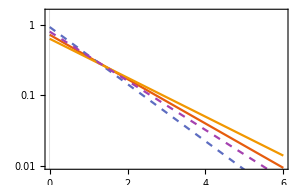

```mathematica
plotrange={{0,6},{0.01,1.5}};
framelabel={xlabelpt2,ylabelpt2};
legends={latex411,latex411bar,latex431,latex431bar};
d411color=pltcolors[[1]];
d411barcolor=pltcolors[[2]];
d431color=pltcolors[[3]];
d431barcolor=pltcolors[[4]];
plotlegends=Placed[LineLegend[{d411color,{Dashed,d411barcolor},d431color,{Dashed,d431barcolor}},legends,Spacings->0.01,LegendLayout->{"Column",2},LegendMarkerSize->16
],{0.825,0.825}];
imagesize={300,Automatic};
frametickstyle=Directive[Black];
imagepadding={{60,3},{40,1}};
scalingfunctions={"Linear","Log"};
b411=0.7224411;
b431=0.63424038;
b411bar=0.92910691;
b431bar=0.80034524;
newplot411=Plot[b411*Exp[-b411*x],{x,0,6},PlotRange->All,PlotStyle->d411color,ScalingFunctions->scalingfunctions];
newplot411bar=Plot[b411bar*Exp[-b411bar*x],{x,0,6},PlotRange->All,PlotStyle->{Dashed,d411barcolor},ScalingFunctions->scalingfunctions];
newplot431=Plot[b431*Exp[-b431*x],{x,0,6},PlotRange->All,PlotStyle->d431color,ScalingFunctions->scalingfunctions];
newplot431bar=Plot[b431bar*Exp[-b431bar*x],{x,0,6},PlotRange->All,PlotStyle->{Dashed,d431barcolor},ScalingFunctions->scalingfunctions];
bg=Plot[{,,,},{x,0,6},ScalingFunctions->scalingfunctions,PlotTheme->"Scientific",PlotRange->plotrange,AspectRatio->1/GoldenRatio,PlotLegends->plotlegends,FrameLabel->framelabel,ImageSize->imagesize,ImagePadding->imagepadding,FrameTicksStyle->frametickstyle];
plotexp=Show[bg,newplot411,newplot411bar,newplot431,newplot431bar]
Export["/home/sane/mainhnlchain/hnlchain/paperHNL/plots/plot-fitpT2Dall.pdf",plotexp];
```

### Data old

Se usaba cuando se realizaba el histograma en python y luego es importaban los bines y alturas.
Ahora todo eso lo realiza mathematica.

```mathematica
xf=Import[NotebookDirectory[]<>"xf.dat"];
pt2=Import[NotebookDirectory[]<>"pt2.dat"];
```

```mathematica
xftable={}; (*411, 431, 411bar, 431bar*)
Do[
xdata=Table[xf[[i,1]]+(xf[[i,2]]-xf[[i,1]])/xf[[i,3]]*j,{j,0,xf[[i,3]]-1}];
ydata=Table[xf[[i,j]],{j,4,xf[[i,3]]+3}];
auxtable=Table[{xdata[[j]],ydata[[j]]},{j,1,Dimensions[xdata][[1]]}];
AppendTo[xftable,auxtable]
,{i,1,4}]
pt2table={}; (*411, 431, 411bar, 431bar*)
Do[
xdata=Table[pt2[[i,1]]+(pt2[[i,2]]-pt2[[i,1]])/pt2[[i,3]]*j,{j,0,pt2[[i,3]]-1}];
ydata=Table[pt2[[i,j]],{j,4,pt2[[i,3]]+3}];
auxtable=Table[{xdata[[j]],ydata[[j]]},{j,1,Dimensions[xdata][[1]]}];
AppendTo[pt2table,auxtable]
,{i,1,4}]
```